InterpolatingFunction::dmval: Input value {0.0000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

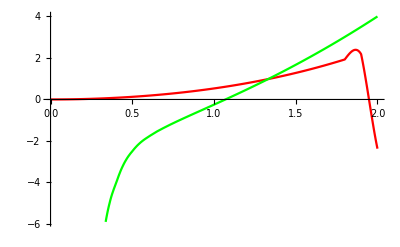

```mathematica
(* Matrix Dimensions *)
(* From HydrogenIon-2D-6.tex  *) 


(* Mathieu's eigenvalues *)

eigenM[p_,n_Integer, index_Integer, evenOdd_Integer]:=Module[{w,q,v, A, mCoeffV0, mCoeffV1,rez},
w:=-A +p^2/2.;      q:= -p^2/4.;
v[nn_]:=(w-nn^2)/q;
mCoeffV0[nn_]:=v[0]+2Simplify[ContinuedFractionK[-1,v[2i],{i,1,nn}]];
mCoeffV1[nn_]:=v[1]-1+Simplify[ContinuedFractionK[-1,v[2i+1],{i,1,nn}]];

rez =If[EvenQ[evenOdd],
	NSolve[mCoeffV0[n]==0,{A},Reals],
	NSolve[mCoeffV1[n]==0,{A},Reals]];
rez = Sort[A  /. rez, Abs[#2]> Abs[#1]&];
rez[[index]]
];

(* L Matrix *)
makeMatrixL[max_, R_]:=Module[{matrix, d,lSum},
d[m_,n_]:=KroneckerDelta[m,n];
matrix = Table[0,{i,1,max}];
	lSum[m_,k_] := ((-2)p k(2k+1)-(2p-1)k^2-4p k +(2R-p)(2k+1)-p -p^2+2R)d[m,k]+(2p k(k+1)-(2R-p)(k+1))d[m,k+1]+(2p k^2+(2p-1)k(2k-1) +(4p-2)k -(2R-p)k)d[m,k-1] -(2p-1)k(k-1)d[m,k-2]+
Sum[d[m,i],{i,0,k-1}];	
	
Do[
matrix[[m+1]] = Table[(-1)lSum[m,k],{k,0,max-1}],
{m,0,max-1}
];
matrix
];

makeMData[pRange_List, R_,n_Integer,index_Integer,evenOdd_Integer] := Module[{data,a},
data=Map[(a = eigenM[#,n,index,evenOdd];{#,a}) &, pRange];
data
];

(* L Matrix *)
makeLData[pRange_List,R_,n_Integer, index_Integer]:=Module[{matrixL,eigenData,a},
matrixL = makeMatrixL[n,R] ;
eigenData  = Map[(a = Sort[Select[ Eigenvalues[N[matrixL/.p->#]],Im[#]==0.&]][[index]]; {#,a}) &, pRange];
eigenData
];

pRange = Range[0.1,5,.1];
R = 1;
(* returns {p,A} *)
eigenMData= makeMData[pRange, R,3,1,0];
eigenLData = makeLData[pRange, R, 20,1];

 mFunc = (eigenMData // Interpolation) ; 
lFunc  = (eigenLData // Interpolation) ;

(* Even - Odd in M covers 1sg+ and 2pu+ *)



Plot[{mFunc[x],lFunc[x]},{x,0,2}, PlotStyle->{Red, Green}]
```

```mathematica
(* value of p *)
pe = x /.FindRoot[mFunc[x] == lFunc[x],{x,1}];


Print["Ground State energies:"]

(* value of A *)
a1= mFunc[pe];
a2= lFunc[pe];

Print["p = ",pe]

Print["A m = ",a1]
Print["A l = ",a2]

ee = -2(pe/R)^2;

Print["E = ", ee]
```

Ground State energies:

p = 1.33111

A m = 0.982013

A l = 0.982013

E = -3.54368